# Take Home Final Report

## By Taylor Graham

## Problem 1

### Question 1:

The first thing I had to do was to simply plug in all of the data into Mathematica so that I had something useful to work with.  I did this by just copying line by line from 	the .txt file provided, and entered those lines into an array.  I then split that huge data array up into the different respectful variables, EX,ECAB,MET,GROW,YOUNG,OLD, and WEST.  The next task was to evaluate the different dependent variables compared against the dependent variable.  I originally did this by just plotting the data for a independent variable and the dependent variable on the same graph, but this turned out to be less useful than I anticipated.  Next was to plot the two different variables as a scatter plot, so you can easily see the correlation between variables.

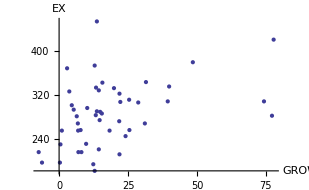
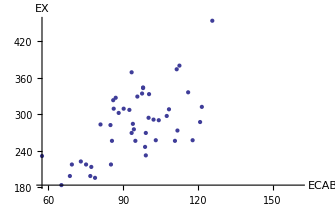

Out of all six plots, only two really appeared to have a linear correlation, and one was kind of a stretch at that.  I have included the plots of ECAB vs EX, which has the highest linear correlation, as well as GROW vs EX, which could possibly be considered constant, but I threw it in there to make it more interesting!

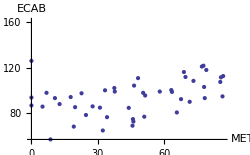
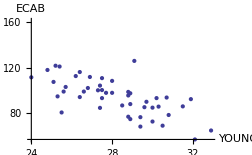
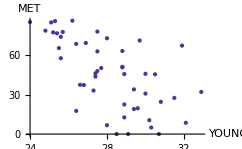
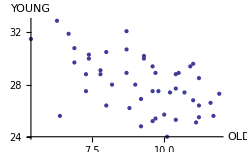

When evaluating the relationships between the dependent variables, I found that the YOUNG dataset causes the most colinearity overall, which I thought was interesting.  The graphs above highlight the most colinear variables, though the first two have a pretty small correlation.

### Question 2:

Next I was tasked with finding the regression model for this data, which involves finding the 6 different regression coefficients, as well as the intercept.  Luckily enough, Mathematica will do all of the hard work for me, I just had to set it up!  I had to modify how my data was formatted (put y at the end of each array instead of at the beginning).  Mathematica has this really nice built in function that will estimate linear models for you, given an input array and all of the variable names.  I used this method to come up with the lovely formula for the multiple regression model.

OverHat[EX]=356.182 + 1.4185 ECAB - 0.660153 MET + 0.57159 GROW - 6.67466 YOUNG - 1.85507 OLD + 35.4723 WEST

I' m surprised by the last parameter coefficient, for western states.  This means that western states can expect an average of $35.5 more per capita expendatures compared to eastern states.  I fully expected both ECAB and MET to have the biggest effect on the expendatures, But it seems like those two variables have a relitavely small effect on the final outcome.  Even the population age has a greater effect, where high amounts of either young or old people in a state can sort of stunt the expendature totals.

### Question 3:

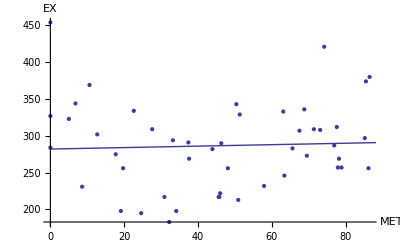
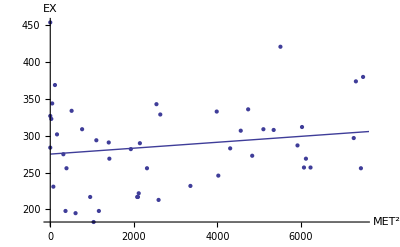
For part 3 I decided to add MET^2 to the regression model, so that it would hopefully account for the nonlinearity of the correlation between MET and EX.  Following is a scatter plot of MET^2 vs EX, and you can start to see a very small positive linear correlation between the two variables now. 
-Graphics-           -Graphics-

The regression equation is as follows

OverHat[EX]=119.118+1.39542 ECAB-3.04214 MET+0.695336 GROW+0.607602 YOUNG+4.12078 OLD+34.0731 WEST+0.030914 (MET^2)^

I would say that this model is less accurate compared to the original one that I came up with in part 2.  For one thing, the coefficient before MET is now negative, so having a larger population means lower expendatures, which is opposite from before.  The opposite observation can be made for the young and old variables; they now have a positive effect on expendatures, where it was negative before.  None of this stuff gets accounted for by the MET^2 variable, as its coefficient is a measly 0.03.

### Question 4:

Question 4 asks us to take the regression model from part 3, and remove any variables that have a large p-value, until none of the p-values are greater than 0.05.  I started with the regression model from part 2, because I feel that that was a better model for me to work with initially.  Mathematica has another nice function to evaluate the parameters p-values for a linear model, so I used that to determine which parameter had the highest p-value.  Initially, it was the WEST parameter that had the highest p-value, at .79, so I got rid of that value first!  Next I performed another linear analysis to get an updated model without the WEST parameter, and recalculated p-values on this new model.  Again there were large p-values, and I chose to eliminate the OLD parameter, as it had a p-value of .91.  I repeat this process a third time, this time eliminating the ECAB parameter with its p-value of .13, were getting close!  I performed a linear regression one more time, and reached my final model, as all parameters have p-values well under 0.05.

OverHat[EX]=668.821+1.52654 GROW-0.982591 MET-12.9968 YOUNG

Final p-values for {GROW, MET, YOUNG, EX}

{9.85785×10^-6,0.0117987,0.000824996,0.00486014}

The fact that all of the remaining p-values are well below 0.05 indicates that we can reject the null hypothesis.  This means that we can have confidence that the new model is better than the one calculated in question 3.

### Question 5 :

I did my hypothesis test by calculating both f and F for each of the three variables that I removed in part 4.  My results were that for the first two tests, we can still accept our hypothesis, meaning that the variable removal is appropriate.  This means that both WEST and OLD can safely be removed from our mode.  However, on my third test, the one on ECAB, we should reject the hypothesis, as f > F.  This means that ECAB should still be included in the model! So our model formula is now:

OverHat[EX]=229.906+1.68092 ECAB+0.76161 GROW-0.830069 MET-2.91085 YOUNG

### Question 6:

I had to do this part in R, as I couldnt find a method in Methematica that would calculate the model for you.

```mathematica
step(null, scope=list(lower=null, upper=full),direction="forward")
Start:  AIC=391.79                                       Step:  AIC=357.27
EX ~ 1                                                   EX ~ ECAB + WEST

        Df Sum of Sq    RSS    AIC                               Df Sum of Sq   RSS    AIC
+ ECAB   1     69845  91577 366.58                       <none>                72351 357.27
+ GROW   1     26366 135056 385.23                       + MET    1   2194.71 70156 357.79
+ WEST   1     22231 139191 386.68                       + GROW   1   1273.93 71077 358.42
+ YOUNG  1     13948 147473 389.45                       + OLD    1     63.82 72287 359.23
<none>               161422 391.79                       + YOUNG  1     58.55 72292 359.23
+ MET    1       415 161007 393.66
+ OLD    1        85 161336 393.76

Step:  AIC=366.58
EX ~ ECAB

        Df Sum of Sq   RSS    AIC
+ WEST   1   19226.5 72351 357.27
+ MET    1    9237.1 82340 363.48
<none>               91577 366.58
+ YOUNG  1    2176.1 89401 367.42
+ GROW   1    2110.2 89467 367.46
+ OLD    1       6.4 91571 368.58


Call:
lm(formula = EX ~ ECAB + WEST)

Coefficients:
(Intercept)         ECAB         WEST  
    102.311        1.696       40.059 


*Note, you get the same formula if you perform the step backwards, or both directions.  
Forward just gives the fewest results (and thus is the cleanest for using here)
```

So the optimal formula that R found is:

OverHat[EX]=102.311+1.696ECAB+40.059WEST

This model does not match the one I calculated in part 4, or any other model I have calculated either.  Its interesting because in part 4, both ECAB and WEST had the highest p values, causing me to eliminate them first, but acording to R, they are the two that should stay.  Just thinking about what the parameters actually reprsent, it seems like this model is less accurate than the one I caluclated.  For one thing, relying heavily on the WEST parameter seems wrong, since that is just a binary variable (1 or 0).  States in the east will get a $40 penalty according to this model, soley because they are in the east.  In reality, the difference betweeen eastern and western states is not this drastic.  This model does make me happy about putting an emphasis on ECAB however.  I thought since the beginning of this problem that ECAB should have the largest effect on the state expendatures, just based off of the definition of what ECAB is: economic ability.  It makes sense to me that a state with a higher economic ability will have a larger amount of expendatures, as their market is fluxuating more.

### Question 7

I think that the model in part 6 is more accurate than the one in part 4, mainly because of the inclusion of ECAB into the model, which I think is an imporntant factor.  Its pretty rediculous how different the models are, each one has completly unique variables in it, but they both are set to model the same set of data.

### Question 8

My favorite model so far is actually the one calculated in part 5

OverHat[EX]=229.906+1.68092 ECAB+0.76161 GROW-0.830069 MET-2.91085 YOUNG

I chose this one because it relies on ECAB for a good amount of the expendatures, while not including the excessive weight of the western states that occurs in the model from part 6.

### Question 9

The 24 th entry in our data has a GROW value of 77.2, which is well above its average of 18.6.  I am going to remove this data point and see if it has any menaingful effect on the overall model.  I also found two more GROW outliers, at 77.8 and 74.3. The resulting new model is

OverHat[EX]=-17.7251+2.8681 ECAB+0.988889 GROW-0.885007 MET+1.90303 YOUNG

I would say that based off of the new model, you need the outliers in the data to sort of balance it out.  In this particular scenario, those GROW outliers that I removed were actual amounts that a states population changed in the 10 year period.  There may have been only three states that grew by this amount (>70), but I think that the data is still necessary and relevant.

## Problem 2

### Question 1:

This question included the main chunk of caclulations for Problem 2.  Our task was to calculate a bunch of useful data given any input array of dependent variables and the output array of independent variables, named X and Y.  I have included the (very clean) function code for you to look at.

```mathematica
func = Function[{argX, argY}, 
(* Calculating the β coeffiients using a simple Least Squares Equation *)
β̂ = Dot[Inverse[Dot[Transpose[argX], argX]], Dot[Transpose[argX], argY]];  
   Print[ "Ŷ = ", β̂[[1]] + β̂[[2]]*"ECAB" + β̂[[3]]*"MET" + β̂[[4]]*"GROW" + β̂[[5]]*"YOUNG" + β̂[[6]]*"OLD" + β̂[[7]]*"WEST"];

(* Just print averages of each parameter *)   
Print["parameter estimates: ", X̄ = {Mean[Transpose[X][[2]]], Mean[Transpose[X][[3]]], Mean[Transpose[X][[4]]], 
      Mean[Transpose[X][[5]]], Mean[Transpose[X][[6]]], Mean[Transpose[X][[7]]]}];
(* Had to calculate the std err for each element, which is the square root of the variance *)   
Print["std err's: ", {Sqrt[Variance[Transpose[X][[2]]]], Sqrt[Variance[Transpose[X][[3]]]], Sqrt[Variance[Transpose[X][[4]]]], 
     Sqrt[Variance[Transpose[X][[5]]]], Sqrt[Variance[Transpose[X][[6]]]], N[Sqrt[Variance[Transpose[X][[7]]]]]}];

(* T values calculated by dividing β_i by the standard deviation of β *)   
Print["T-values: ", {β̂[[2]]/StandardDeviation[β̂], β̂[[3]]/StandardDeviation[β̂], β̂[[4]]/StandardDeviation[β̂],
	β̂[[5]]/StandardDeviation[β̂], β̂[[6]]/StandardDeviation[β̂], β̂[[7]]/StandardDeviation[β̂]}];

(*P values calculated with x̄-Subscript[μ, o]/(s/√n) *)
Print["P-values: ",{(X̄[[1]])*Sqrt[48]/StandardDeviation[Transpose[X][[2]]],(X̄[[2]])*Sqrt[48]/StandardDeviation[Transpose[X][[3]]], 
	(X̄[[3]])*Sqrt[48]/StandardDeviation[Transpose[X][[4]]], (X̄[[4]])*Sqrt[48]/StandardDeviation[Transpose[X][[5]]], 
	(X̄[[5]])*Sqrt[48]/StandardDeviation[Transpose[X][[6]]], (X̄[[6]])*Sqrt[48]/StandardDeviation[Transpose[X][[7]]]}];

(* SSE and SST, calculated with SSE=∑(Subscript[y, i]-Subscript[ŷ, i])^2 and SST=∑(Subscript[y, i]-ȳ)^2 *)   
SSE = 0;
SST = 0;
For[i = 1, i < 49, i++, SSE = SSE + (Y[[i]]-(β̂[[1]]+β̂[[2]]*Transpose[X][[2, i]]+β̂[[3]]*Transpose[X][[3, i]]+β̂[[4]]*Transpose[X][[4, i]]+
	β̂[[5]]*Transpose[X][[5, i]]+β̂[[6]]*Transpose[X][[6, i]]+β̂[[7]]*Transpose[X][[7, i]]))^2];
Print["SSE = ", SSE];
For[i = 1, i < 49, i++, SST = SST + (Y[[i]] - Mean[Y])^2];

(* R^2, Subscript[R, α]^2, and the F-statistic can all be calculated using SSE and SST, which I already have! *)
Print["R^2 = ", 1 - SSE/SST];
Print["R_α^2 = ", 1 - (SSE/(48 - 6 - 1))/(SST/(48 - 1))];
Print["F-Statistic = ", ((SST - SSE)/6)/(SSE/(48 - 6 - 1))];
];
```

As you can tell, I did not output the first part in a table, mainly because I couldn' t figure out how to format Mathematica output very well.  I had a little trouble with defining functions in Mathematica, because it’s not very intuitive.  Regardless, all of the necessary output is there, so I figured it wasn’t a huge deal.

### Question 2

For this question I just replaced all of the MET values that I have been using with the respective MET_categ value, which ranged from 1 to 6.  The resulting MET_categ array is as follows:

MET2 = {2, 2, 1, 6, 6, 6, 6, 6, 6, 5, 6, 4, 5, 5, 4, 6, 4, 3, 3, 4, 2, 3, 4, 5, 4, 1, 4, 3, 4, 1, 1, 3, 3, 1, 2, 3, 5, 2, 5, 2, 1, 1, 1, 5, 5, 4, 5, 6};

### Question 3

Now, using my lovely function that I made eralier in question 1, I was able to evaluate the regression model including the updated MET_categ values.  I did this by building a new X array which includes the new MET_categ array instead of the old MET values.  I kept the standard model with all the parameters to make calculations easier.  I could then just plug my two arrays (XNEW and Y) into my function and get some output!

Ŷ = 354.978 + 1.42347 ECAB + 0.551514 GROW - 10.2371 MET - 1.69596 OLD + 33.2001 WEST - 6.39627 YOUNG
List of parameter estimates : {96.7542, 46.1687, 18.7292, 28.1146, 9.2125, 1/2}
List of std err' s : {22.2528, 26.9388, 18.8747, 2.14853, 1.63936, 0.505291}
List of T-values : {0.0106339, -0.0764753, 0.00412005, -0.047783, -0.0126696, 0.248019}
List of P-values : {30.1235, 11.8738, 6.87477, 90.6591, 38.9335, Sqrt[47]}
SSE = 1.2283*10^7
R^2 = -74.6011
R_α^2 = -85.6647
F-Statistic = -6.74295

### Question 4

From the results in question 3, I am now able to build a new regression model with the update MET_categ values.

Ŷ = 354.978 + 1.42347 ECAB + 0.551514 GROW - 10.2371 MET_categ - 1.69596 OLD + 33.2001 WEST - 6.39627 YOUNG

Here was my original model

OverHat[EX]=356.182 + 1.4185 ECAB - 0.660153 MET + 0.57159 GROW - 6.67466 YOUNG - 1.85507 OLD + 35.4723 WEST

This formula gives the MET_categ a higher weight than the originl MET, which makes sense, because the magnitude of MET_categ values, ranging from 1 to 6, are typically smaller than the MET values, which can range from 0 to 100.  Because of MET_categ’s increase in weight, all of the weights for the other parameters dropped ever so slightly to compensate.  I still expected ECAB to have the largest effect on the total expendatures, at least, thats what I assume based off of its name.  However, it has one of the smaller weights attached to it.

### Question 5

Honestly, I think you do lose a little bit of information when using a categorical covariate vs a contunious covariate.  The categorical values are more broad (values ranging from 1 to 6) than the contunious values (values ranging from 0 to 100).  Although the categorical covariate has a larger weight to make up for its smaller values, I still think you lose some accuracy in the data.  For example, using a contunious covariate, a MET value of 46.2 will give you a different result than a MET value of 59.9, but both of those MET values get smashed into the categorical value 4 (45 UnderBar[<] MET < 60). I guess the benefit is that it is a little easier to work with, because you only have 6 possibilities rather than 100.  If you could get the computer to do this coversion for you (unlike what I did), it would become more efficient for finding the multiple regression model.